## 01

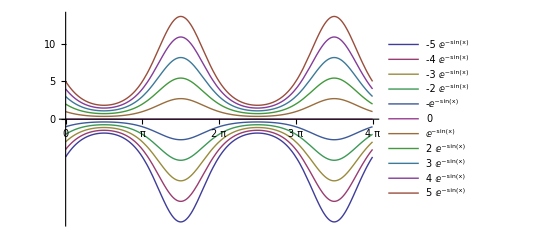

```mathematica
ClearAll;
p=DSolve[y'[x]==-Cos[x]*y[x],y[x],x];
eq1=p[[1,1,2]];
t1=Table[eq1/.{C[1]->i},{i,-5,5}];
Plot[t1,{x,0,4Pi},Ticks->{{0,Pi,2Pi,3Pi,4Pi},{0,5,10}},PlotLegends->"Expressions"]
```

## 02

```mathematica
ClearAll;
Exit[]
```

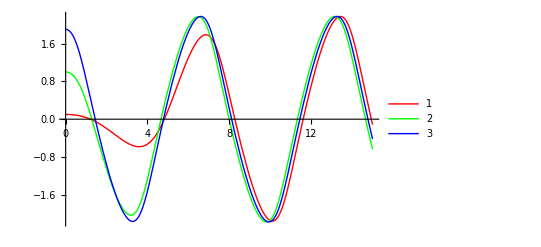

```mathematica
eq2=x''[t]+(1/3*(x'[t])^2-1)*x'[t]+x[t]==0;
init={{x[0]==0.1,x'[0]==0},{x[0]==1,x'[0]==0},{x[0]==1.9,x'[0]==0}};
t2=Table[NDSolve[{eq2,init[[i]]},x[t],{t,0,15}],{i,1,3}];
Plot[Evaluate[x[t]/.t2],{t,0,15},PlotStyle->{Red,Green,Blue},PlotLegends->{"1","2","3"}]
```

## 03

```mathematica
ClearAll;
Exit[]
```

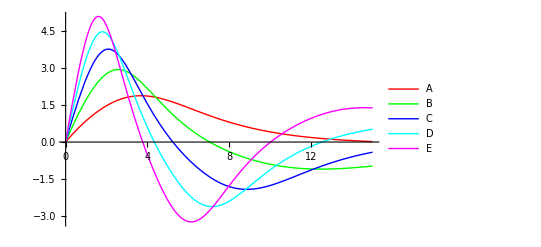

```mathematica
m=1;k=.3;a=.04;
eq3=m*x''[t]+k*x'[t]+a*x[t]^3==0;
init=Table[{x[0]==0,x'[0]==i},{i,1,5}];
t3=Table[NDSolveValue[{eq3,init[[i]]},x[t],{t,0,15}],{i,1,5}];
Plot[Evaluate[t3],{t,0,15},PlotStyle->{Red,Green, Blue,Cyan, Magenta},PlotLegends->{"A","B","C","D","E"}]
```

## 04

```mathematica
Exit[]
```

```mathematica
Clear[x,y,z,t]
```

```mathematica
s1=10;b1=8/3;r1=28;
eq4={x'[t]==s1*(y[t]-x[t]),
y'[t]==r1*x[t]-y[t]-x[t]*z[t],
z'[t]==x[t]*y[t]-b1*z[t]};
init={x[0]==10,y[0]==10,z[0]==10};
t4=NDSolveValue[{eq4,init},{x[t],y[t],z[t]},{t,0,50}];
ParametricPlot3D[Evaluate[t4],{t,0,50}]
```

-Graphics3D-

## 05

```mathematica
Exit[]
```

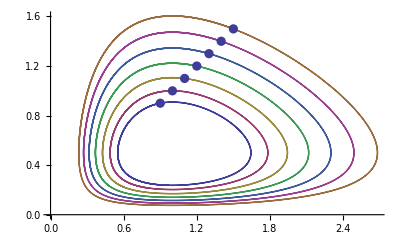

```mathematica
a=2/3;b=4/3;c=1;d=1;
eq5={{x'[t]==x[t]*(a-b*y[t])},{y'[t]==y[t]*(c*x[t]-d)}};
init=Table[{x[0]==i,y[0]==i},{i,.9,1.5,.1}];
t5=Table[NDSolveValue[{eq5,init[[i]]},{x[t],y[t]},{t,0,20}],{i,1,Length[init]}];
A1=ParametricPlot[t5,{t,0,20}];
A2=ListPlot[Table[{i,i},{i,.9,1.5,.1}],PlotStyle->PointSize[.05/3]];
Show[A1,A2]
```

## 06

```mathematica
Clear[x,t,u]
Exit[]
```

```mathematica
Print["Given equation"]
eq6=D[D[u[x,t],x],x]==D[D[u[x,t],t],t]
Print["Initial Condtion"]
init={u[x,0]->3*x,Derivative[0,1][u][x,0]->Sin[2*x]}
Print["Laplace Transform"]
Lp=LaplaceTransform[eq6,t,s]/.init
sol=DSolve[Lp,u[x,t],{x}][[1,1,2]];

u[x,s]==sol
Print["Inverse Laplace Transform"]
u[x,t]==InverseLaplaceTransform[sol,s,t]
Plot3D[p2,{t,0,2},{x,-2,2},ColorFunction->"Rainbow"]
```

Given equation

u^(2,0)[x,t]==u^(0,2)[x,t]

Initial Condtion

{u[x,0]→3 x,u^(0,1)[x,0]→Sin[2 x]}

Laplace Transform

LaplaceTransform[u^(2,0)[x,t],t,s]==-3 s x+s^2 LaplaceTransform[u[x,t],t,s]-Sin[2 x]

u[x,s]==ⅇ^(s x) C[1]+ⅇ^(-s x) C[2]+(12 x+3 s^2 x+s Sin[2 x])/(4+s^2)

Inverse Laplace Transform

u[x,t]==C[2] DiracDelta[t-x]+C[1] DiracDelta[t+x]+3 x (DiracDelta[t]-2 Sin[2 t])+6 x Sin[2 t]+Cos[2 t] Sin[2 x]

-Graphics3D-

## 03

```mathematica
Exit[]
```

```mathematica
Clear[x]
```

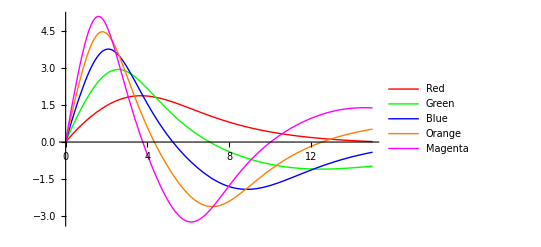

```mathematica
m=1;k=.3;a=.04;
init=Table[{x[0]==0,x'[0]==i},{i,1,5}];
eq31=m*x''[t]+k*x'[t]+a*x[t]^3==0;
t31=Table[NDSolveValue[{eq31,init[[i]]},x[t],{t,0,15}],{i,1,Length[init]}];
Plot[Evaluate[t31],{t,0,15},PlotStyle->{Red,Green,Blue,Orange,Magenta},PlotLegends->{"Red","Green","Blue","Orange","Magenta"}]
```

## 04

```mathematica
Exit[]
```

```mathematica
o=10;b=8/3;p=28;
eq41={x'[t]==o*(y[t]-x[t]),y'[t]==p*x[t]-y[t]-x[t]*z[t],z'[t]==x[t]*y[t]-b*z[t]};
init={x[0]==10,y[0]==10,z[0]==10};
t41=NDSolveValue[{eq41,init},{x[t],y[t],z[t]},{t,0,50}];
ParametricPlot3D[Evaluate[t41],{t,0,50}]
```

{x'[t]==10 (-x[t]+y[t]),y'[t]==28 x[t]-y[t]-x[t] z[t],z'[t]==x[t] y[t]-(8 z[t])/3}

-Graphics3D-

## 05

```mathematica
Exit[]
```

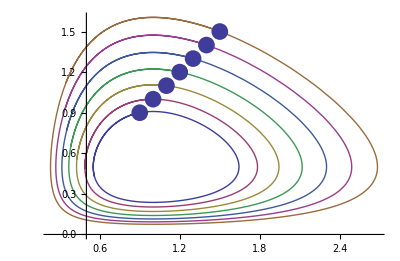

```mathematica
a=2/3;b=4/3;p=1;del=1;
eq51={x'[t]==x[t]*(a-b*y[t]),y'[t]==y[t]*(del*x[t]-p)};
init=Table[{x[0]==i,y[0]==i},{i,.9,1.5,.1}];
t51=Table[NDSolveValue[{eq51,init[[i]]},{x[t],y[t]},{t,0,20}],{i,1,Length[init]}];
plot1=ParametricPlot[t51,{t,0,10}];
plot2=ListPlot[Table[{i,i},{i,.9,1.5,.1}],PlotStyle->PointSize[.03]];
Show[plot1,plot2]
```

## 04

```mathematica
Exit[]
```

```mathematica
o=10;b=8/3;p=28;
eq42={x'[t]==o(y[t]-x[t]),y'[t]==p*x[t]-y[t]-x[t]*z[t],z'[t]==x[t]*y[t]-b*z[t]};
init={x[0]==0,y[0]==10,z[0]==10};
t42=Evaluate[NDSolveValue[{eq42,init},{x[t],y[t],z[t]},{t,0,50}]];
ParametricPlot3D[t42,{t,0,50}]
```

-Graphics3D-

## 05

```mathematica
Exit[]
```

{x'[t]==x[t] (2/3-(4 y[t])/3),y'[t]==(-1+x[t]) y[t]}

{{x[0]==0.9,y[0]==0.9},{x[0]==1.,y[0]==1.},{x[0]==1.1,y[0]==1.1},{x[0]==1.2,y[0]==1.2},{x[0]==1.3,y[0]==1.3},{x[0]==1.4,y[0]==1.4},{x[0]==1.5,y[0]==1.5}}

{{InterpolatingFunction[{{0.,20.}},<>][t],InterpolatingFunction[{{0.,20.}},<>][t]},{InterpolatingFunction[{{0.,20.}},<>][t],InterpolatingFunction[{{0.,20.}},<>][t]},{InterpolatingFunction[{{0.,20.}},<>][t],InterpolatingFunction[{{0.,20.}},<>][t]},{InterpolatingFunction[{{0.,20.}},<>][t],InterpolatingFunction[{{0.,20.}},<>][t]},{InterpolatingFunction[{{0.,20.}},<>][t],InterpolatingFunction[{{0.,20.}},<>][t]},{InterpolatingFunction[{{0.,20.}},<>][t],InterpolatingFunction[{{0.,20.}},<>][t]},{InterpolatingFunction[{{0.,20.}},<>][t],InterpolatingFunction[{{0.,20.}},<>][t]}}

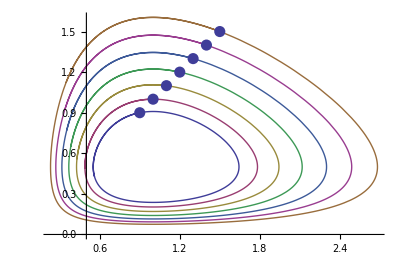

```mathematica
a=2/3;b=4/3;c=1;d=1;
eq52={x'[t]==x[t]*(a-b*y[t]),y'[t]==y[t]*(c*x[t]-d)}
init=Table[{x[0]==i,y[0]==i},{i,.9,1.5,.1}]
t52=Evaluate[Table[NDSolveValue[{eq52,init[[i]]},{x[t],y[t]},{t,0,20}],{i,1,Length[init]}]]
Show[ParametricPlot[t52,{t,0,10}],ListPlot[Table[{i,i},{i,.9,1.5,.1}],PlotStyle->PointSize[.02]]]
```

## 06

```mathematica
Exit[]
```

```mathematica
eq62=D[D[u[x,t],x],x]==D[D[u[x,t],t],t]
init={u[x,0]->3*x, Derivative[0,1][u][x,0]->Sin[2*x]};
Lp=LaplaceTransform[eq62,t,s]/.init;
sol1=DSolve[Lp,u[x,t],x][[1,1,2]];

ILp=InverseLaplaceTransform[sol1,s,t]
Plot3D[ILp,{t,0,2},{x,-2,2},ColorFunction->"Rainbow"]
```

u^(2,0)[x,t]==u^(0,2)[x,t]

C[2] DiracDelta[t-x]+C[1] DiracDelta[t+x]+3 x (DiracDelta[t]-2 Sin[2 t])+6 x Sin[2 t]+Cos[2 t] Sin[2 x]

-Graphics3D-